### Trying more asymmetric doubling adaptive searches

```mathematica
asymdubevosk3 = ParallelTable[
SeedRandom[221130 + j];
AdaptiveCellularAutomaton[<|"Rule"->{0, 3, 1}, "Depth"->1000, 
"MutationFunction"->(RandomRuleMutation[#Rule, 1]&),
 "FitnessFunction"-> (-Total[Abs[Table[CenterArray[#, Max[Length[#],2i+2]&[#]] - CenterArray[Table[1, 2i+2], Max[Length[#],2i+2]]&[CellularAutomaton[#1, {Append[Table[1, i], 2], 0}, {{{60}}}]] , {i, 5}]], 2]&)|>], {j, 60}];
```

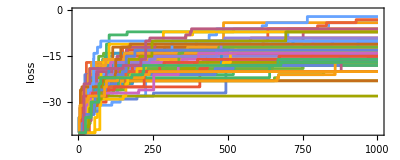

```mathematica
ListStepPlot[#[[All, "Fitness"]]&/@ asymdubevosk3, Frame->True, FrameLabel->{"steps", "loss"}, AspectRatio->.4]
```

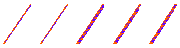
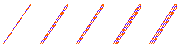
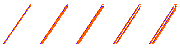
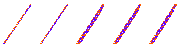
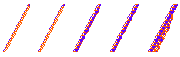
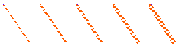
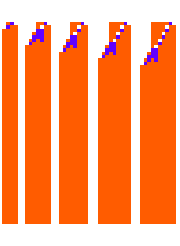
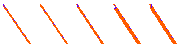
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
GraphicsRow[ArrayPlot[#, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]}]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0}, 60], {i, 5}], ImageSize->Small]&[#[[-1]]]&/@ asymdubevosk3
```

```mathematica
ListLinePlot[Join[{Table[ 2i+2, {i, 50}]}, Tooltip[Count[#, 1]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0},{{{60}}}], {i, 50}], ArrayPlot[CellularAutomaton[#Rule,{Append[Table[1, 15], 2], 0},60]]]&/@ asymdubevosk3[[All, -1]]], PlotHighlighting->None, PlotStyle->Prepend[Table[Orange, 60], Blue], Frame->True, FrameLabel->{"Input", "Output"}, AspectRatio->.4]
```

-Graphics-

```mathematica
MinimalBy[asymdubevosk3[[All, -1]], Total[Abs[Table[ 2i+2, {i, 50}] - (Count[#, 1]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0},{{{60}}}], {i, 50}])]]&, 10]
```

{<|Rule→{7543256137557,3,1},Fitness→-15|>,<|Rule→{2626843921155,3,1},Fitness→-23|>,<|Rule→{3287424141180,3,1},Fitness→-13|>,<|Rule→{765195917886,3,1},Fitness→-2|>,<|Rule→{4744750837374,3,1},Fitness→-3|>,<|Rule→{338856115359,3,1},Fitness→-7|>,<|Rule→{7014686365467,3,1},Fitness→-6|>,<|Rule→{3975352709436,3,1},Fitness→-4|>,<|Rule→{2598179338533,3,1},Fitness→-10|>,<|Rule→{2886337411146,3,1},Fitness→-6|>}

```mathematica
ListLinePlot[Join[{Table[ 2i+2, {i, 50}]}, Count[#, 1]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0},{{{200}}}], {i, 50}]&/@ ], PlotHighlighting->None, PlotStyle->Prepend[Table[Orange, 60], Blue], Frame->True, FrameLabel->{"Input", "Output"}, AspectRatio->.4]
```

-Graphics-

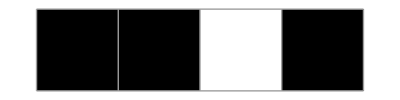
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
ArrayPlot[{#}, Mesh->True]&/@ Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0},{{{60}}}], {i, 10}]&/@ [[{1}]]
```

```mathematica
GraphicsRow[ArrayPlot[#, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]}]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0}, 60], {i, 10}], ImageSize->Small]&/@ [[{1}]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
GraphicsRow[ArrayPlot[#, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]}]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0}, 60], {i, 5}]]&/@ [[{1}]]
```

{-Graphics-}

#### Continuous output of 1s

```mathematica
asymdubevosk3 = ParallelTable[
SeedRandom[221130 + j];
AdaptiveCellularAutomaton[<|"Rule"->{0, 3, 1}, "Depth"->1000, 
"MutationFunction"->(RandomRuleMutation[#Rule, 1]&),
 "FitnessFunction"-> (-Total[Abs[Table[CenterArray[#, Max[Length[#],2i+2]&[#]] - CenterArray[Table[1, 2i+2], Max[Length[#],2i+2]]&[CellularAutomaton[#1, {Append[Table[1, i], 2], 0}, {{{60}}}]] , {i, 5}]], 2]&)|>], {j, 60}];
```